### Premice in ravnine

PREMICE

Premica je eden od osnovnih pojmov geometrije.

Definicija: Premica je neskončen, raven geometrijski objekt.

Na obeh straneh s točkama omejen del premice imenujemo daljica. Če je premica omejena le na eni strani, imenujemo tisti del poltrak. Dve različni premici se sekata v največ eni točki.
Definirajmo daljico v prostoru ℝ^2 s poljubnima dvema točkama.

```mathematica
p = Daljica[{0, 4}, {3, 1}]
```

Daljica[{0,4},{3,1}]

Določimo obliko naše daljice, ki je ravna črta omejena s podanima točkama, in prikažimo njen graf.

```mathematica
Slika[Daljica[AA_, BB_]] := Line[{AA, BB}]
```

```mathematica
Slika[p]
```

Line[{{0,4},{3,1}}]

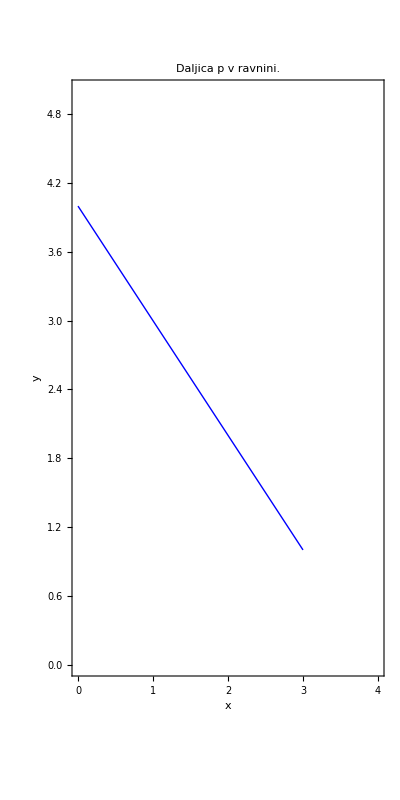

```mathematica
Risba1 = Graphics[{Blue, Slika[p]}, PlotRange->{{0, 4}, {0, 5}}, Axes->True, Frame->True, AspectRatio->2/1, PlotLabel->"Daljica p v ravnini.", FrameLabel-> {x, y}]
```

Ker smo že omenili, da je daljica omejeni del na premici, poiščimo še enačbo nosilke (premica) daljice.

```mathematica
EnacbaPremice[Daljica[AA_, BB_]] := Module[{x1, y1, x2, y2, k, n}, 
{x1, y1} = AA;
{x2, y2} = BB;
k = (y2-y1)/(x2-x1);
n = n /. First[Solve[y1 == x1 * k + n, n]];
y == k * x + n]
```

```mathematica
EnacbaPremice[p]
```

y==4-x

```mathematica
Premica1 = EnacbaPremice[p]
```

y==4-x

```mathematica
ClearAll[Premica]
```

Spodaj je tudi prikazan graf dane premice v koordinatnem sistemu.

```mathematica
y = -x + 4
```

4-x

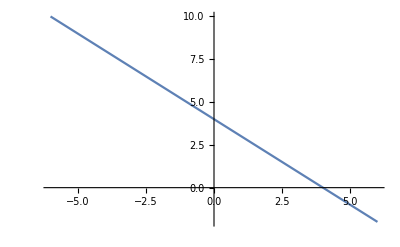

```mathematica
Plot[y, {x, -6, 6}]
```

V splošnem zapisujemo enačbe premic v eksplicitni obliki. Spodaj imamo animacijo premice. Na podlagi spreminjanja koeficienta in začetne vrednosti, lahko vidimo njen položaj v grafu. Koeficient premice pomeni njen naklon v grafu. Spodaj imamo primer, ki prikazuje, da čim se k približuje nič, je premica bolj položna.

{2+x,2+x/2,2+x/3,2+x/4,2+x/5,2+x/6,2+x/7,2+x/8,2+x/9,2+x/10,2+x/11,2+x/12,2+x/13,2+x/14,2+x/15,2+x/16,2+x/17,2+x/18,2+x/19,2+x/20}

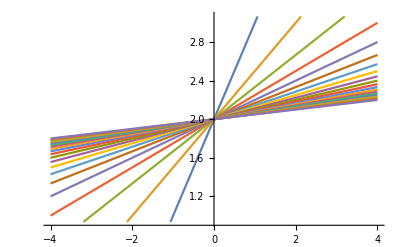

```mathematica
PremiceRazlicnihKoeficientov = Table[1/k x + 2, {k, 20}]
SlikaPremic = Plot[PremiceRazlicnihKoeficientov, {x, -4, 4}]
```

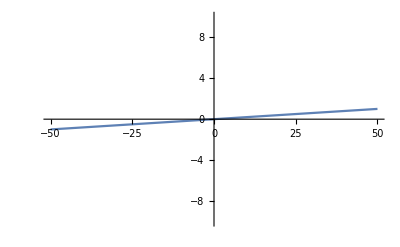

```mathematica
Plot[1/50 x, {x, -50, 50}, PlotRange->{-10, 10}]
```

```mathematica
Manipulate[Plot[k x + n, {x, -8, 8}, PlotRange->{-8, 8}], {k, -3, 3}, {n, -3, 3}]
```

Primer: Podane imamo naslednje tri daljice:

```mathematica
q = Daljica[{-1, 2}, {8, 2}]
```

Daljica[{-1,2},{8,2}]

```mathematica
z = Daljica[{2, -1}, {2, 8}]
```

Daljica[{2,-1},{2,8}]

```mathematica
r = Daljica[{-1, 2/3}, {8, 11/3}]
```

Daljica[{-1,2/3},{8,11/3}]

```mathematica
Slika[q]
```

Line[{{-1,2},{8,2}}]

```mathematica
Slika[z]
```

Line[{{2,-1},{2,8}}]

```mathematica
Slika[r]
```

Line[{{-1,2/3},{8,11/3}}]

Prikazane so tri risbe:
- risba daljice q, katere nosilka je vodoravna premica,
- risba daljice z, katere nosilka je navpična premica,
- risba vseh danih daljic.
Ugotovi, katera pripadajoča premica nima svojega eksplicitnega zapisa?

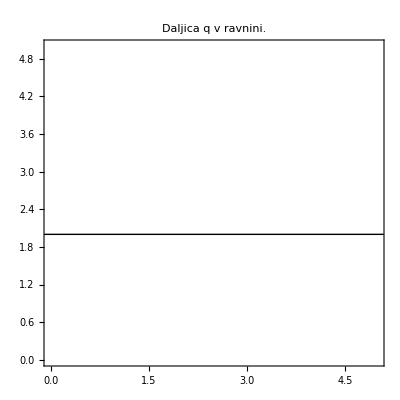

```mathematica
RisbaVodoravna = Graphics[Slika[q], PlotRange-> {{0, 5}, {0, 5}}, Axes->True, Frame->True, AspectRatio->Automatic, PlotLabel->"Daljica q v ravnini."]
```

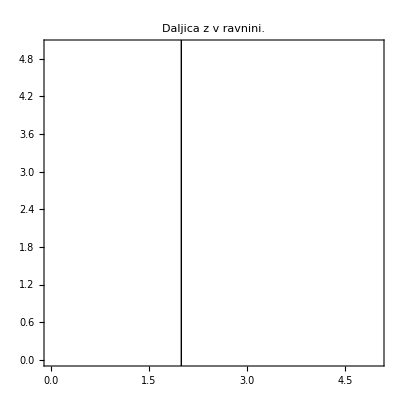

```mathematica
RisbaNavpicna = Graphics[Slika[z], PlotRange-> {{0, 5}, {0, 5}}, Axes->True, Frame->True, AspectRatio->Automatic, PlotLabel->"Daljica z v ravnini."]
```

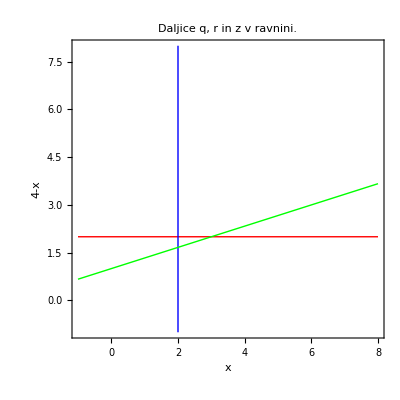

```mathematica
Graphics[{Thick, Red, Slika[q], Blue, Slika[z], Green, Slika[r], PlotRange-> {{0, 5}, {0, 5}}}, Axes->True, Frame->True, AspectRatio->Automatic, PlotLabel-> "Daljice q, r in z v ravnini.", FrameLabel-> {x, y}]
```

Rešitev je navpična premica, ki ni graf nobene funkcije, saj enemu x pripada neskončno mnogo y. Vrednosti spremenljivke y so neodvisne od x. Eksplicitni zapis za take premice ne obstaja.

```mathematica
ClearAll[r]
```

RAVNINE

Ravnina je eden od osnovnih pomov geometrije, ki ga lahko prikažemo v prostoru ℝ^3.

Definicija: Ravnina je ravna neomejena ploskev.

Prikazujemo jo z dano normalo in točko, skozi katero potuje ravnina. Normala je premica, ki je pravokotna na neskončno število ravnin. Točka na normali pa določa natanko eno ravnino.
Definirajmo ravnino r1 s komponentami njene normale in dane točke.

```mathematica
r1 = Ravnina[{-1, -1, -2}, {3/5, 1/2, 29/20}]
```

Ravnina[{-1,-1,-2},{3/5,1/2,29/20}]

```mathematica
ClearAll[Slika1, d, r]
```

```mathematica
SlikaRavnine[Ravnina[n_, v_]] := Hyperplane[n, v]
```

```mathematica
SlikaRavnine[r1]
```

Hyperplane[{-1,-1,-2},{3/5,1/2,29/20}]

Normalo prikažemo kot ravno črto, ki poteka skozi dve točki, skozi dano točko ravnine in točko na normali, ki jo dobimo tako, da prvotni točki prištejemo komponente normale.

```mathematica
SlikaNormale[Ravnina[n_, v_]] :=Arrow[{v, v + n}]
SlikaNormale[r1]
```

Arrow[{{3/5,1/2,29/20},{-2/5,-1/2,-11/20}}]

```mathematica
Risba1 = Graphics3D[{Red, SlikaRavnine[r1], Thick, Blue, SlikaNormale[r1]}, AspectRatio->Automatic, Axes->True]
```

-Graphics3D-

Primer: Imamo podano premico.

Skozi vsako točko obstaja le ena ravnina, katere normala je dana premica.

```mathematica
f[x_] = x
```

x

```mathematica
Manipulate[Plot[f[x], {x, -3, 3}, Epilog->Disk[{x, f[x]}, 0.08]], {x, -3, 3}]
```

Ravnine ene normale so prikazane na naslednjem primeru.

Primer: Podane so tri ravnine v ℝ^3.

Vsaka od njih je vzporedna z osjo x in z, os y pa sekajo pri različnih vrednostih. Ker so medseboj vzporedne, imajo enako normalo, kot vidimo spodaj.

```mathematica
r2 = Ravnina[{0, 1, 0}, {0, 0, 0}]
r3 = Ravnina[{0, 1, 0}, {0, 1, 0}]
r4 = Ravnina[{0, 1, 0}, {0, 2, 0}]
```

Ravnina[{0,1,0},{0,0,0}]

Ravnina[{0,1,0},{0,1,0}]

Ravnina[{0,1,0},{0,2,0}]

```mathematica
SlikaRavnine[r2]
SlikaRavnine[r3]
SlikaRavnine[r4]
```

Hyperplane[{0,1,0},{0,0,0}]

Hyperplane[{0,1,0},{0,1,0}]

Hyperplane[{0,1,0},{0,2,0}]

```mathematica
Risba2 = Graphics3D[{SlikaRavnine[r2], SlikaRavnine[r3], SlikaRavnine[r4], Red, Arrow[{{0, 0, 0}, {0, 3, 0}}]}, AspectRatio->Automatic, Axes->True]
```

-Graphics3D-

Ravnina v ℝ^3 ima tudi svojo enačbo, iz katere se lahko takoj vidijo komponente normale. Z vstavljanjem vrednosti odvisnih spremenljivk (x, y, z) pa računamo točke na naši ravnini.

```mathematica
ClearAll[x, y, z]
```

```mathematica
EnacbaRavnine[Ravnina[n_, v_]] := Module[{a, b, c, x1, y1, z1, d},
{a, b, c} = n;
{x1, y1, z1} = v;
d = d /. First[Solve[d == a*x1 + b*y1 + c*z1, d]];
d == a*x + b*y + c*z]
```

```mathematica
r1
```

Ravnina[{-1,-1,-2},{3/5,1/2,29/20}]

```mathematica
EnacbaRavnine[r1]
```

-4==-x-y-2 z

```mathematica
EnacbaRavnine[r2]
EnacbaRavnine[r3]
EnacbaRavnine[r4]
```

0==y

1==y

2==y

Pri nevzporednih ravninah pa računamo njihove preseke.
Presek dveh nevzporednih ravnin je premica, treh nevzporednih ravnin pa ena sama točka. Spodaj imamo primer treh nevzporednih ravnin. Zapišimo njihove enačbe in točko preseka.

```mathematica
r5 = Ravnina[{1, -1, 1}, {1, 1, 0}]
r6 = Ravnina[{2, 1, -1}, {1, 0, -1}]
r7 = Ravnina[{-1, 2, 1}, {0, 2, 0}]
```

Ravnina[{1,-1,1},{1,1,0}]

Ravnina[{2,1,-1},{1,0,-1}]

Ravnina[{-1,2,1},{0,2,0}]

```mathematica
Er5 = EnacbaRavnine[r5]
Er6 = EnacbaRavnine[r6]
Er7 = EnacbaRavnine[r7]
```

0==x-y+z

3==2 x+y-z

4==-x+2 y+z

```mathematica
PresekRavnin[ravnina1_, ravnina2_, ravnina3_] := {x, y, z} /. First[Solve[{ravnina1, ravnina2, ravnina3}, {x, y, z}]]
```

```mathematica
PresečnaTočka = PresekRavnin[Er5, Er6, Er7]
```

{1,2,1}

```mathematica
SlikaRavnine[r5]
```

Hyperplane[{1,-1,1},{1,1,0}]

```mathematica
SlikaRavnine[r6]
```

Hyperplane[{2,1,-1},{1,0,-1}]

```mathematica
SlikaRavnine[r7]
```

Hyperplane[{-1,2,1},{0,2,0}]

```mathematica
Graphics3D[{SlikaRavnine[r5], SlikaRavnine[r6], SlikaRavnine[r7], Opacity[.8], Sphere[PresečnaTočka, 0.05]}]
```

-Graphics3D-